```mathematica
SetDirectory[NotebookDirectory[]]
Needs["SSS`"]
```

C:\Users\caviness\Documents\Git\SSS-Code\Main

### Accelerated iteration, using one combined long-jump test

(* Combination test, returns result of first test that is applicable, else {} if all tests fail *)

```mathematica
TestForAll[rs:<|"Index"->_,"QCode"->_,"RuleSet"->_|>] := Module[{ans}, 
If[Length[ans=TestForConflictingRules[rs]]>0,Return[ans]];
If[Length[ans=TestForNonSoloIdentityRule[rs]]>0,Return[ans]];
If[Length[ans=TestForRenamedRuleSet[rs]]>0,Return[ans]];
If[Length[ans=TestForNonSoloInitialSubstringRule[rs]]>0,Return[ans]];
If[Length[ans=TestForUnbalancedRuleSet[rs]]>0,Return[ans]];
Return[TestForShorteningRuleSet[rs]]
];
```

<|Index→2,QCode→0,RuleSet→{A→,→A}|> (Repeating):

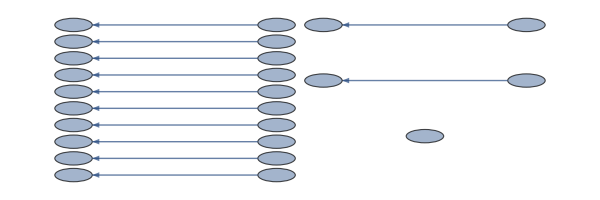
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→4,QCode→2,RuleSet→{A→A}|> (Repeating):

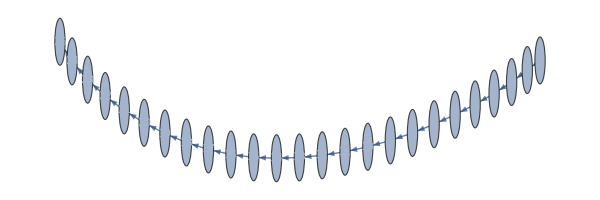
-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

<|Index→10,QCode→03,RuleSet→{A→,→AA}|> (Repeating):

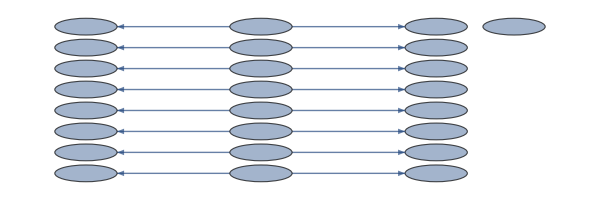
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→20,QCode→23,RuleSet→{A→AA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

<|Index→22,QCode→30,RuleSet→{AA→,→A}|> (Repeating):

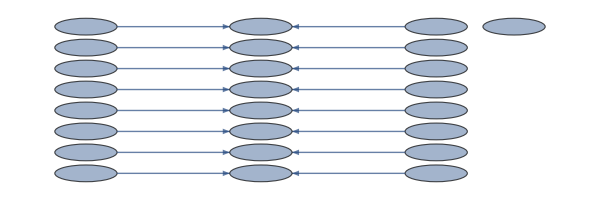
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50,QCode→033,RuleSet→{A→,→AAA}|> (Repeating):

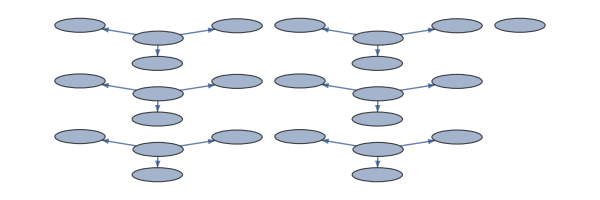
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→110,QCode→303,RuleSet→{AA→,→AA}|> (Repeating):

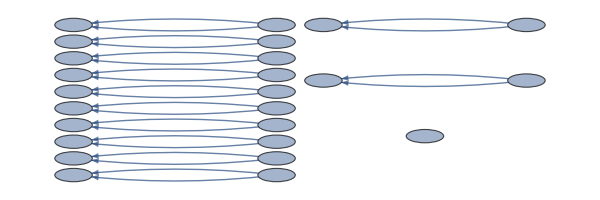
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→112,QCode→310,RuleSet→{AA→,A→,→A}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→118,QCode→321,RuleSet→{AA→A,→A}|> (Repeating):

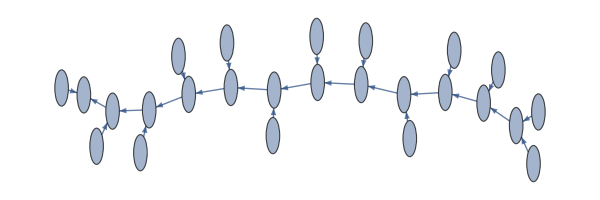
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→120,QCode→323,RuleSet→{AA→AA}|> (Repeating):

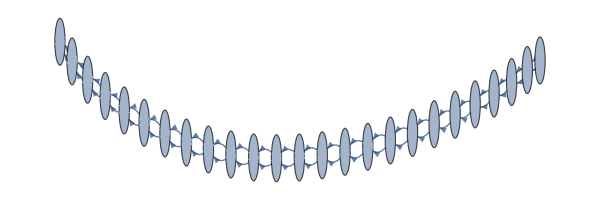
-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

<|Index→122,QCode→330,RuleSet→{AAA→,→A}|> (Repeating):

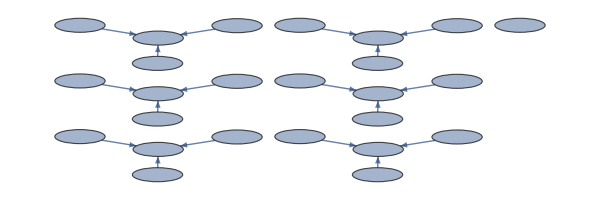
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→250,QCode→0333,RuleSet→{A→,→AAAA}|> (Repeating):

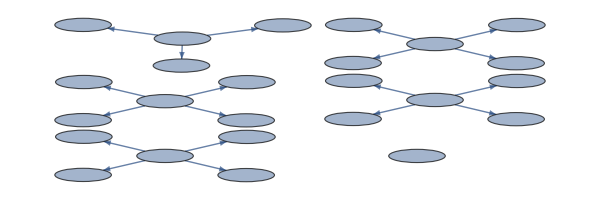
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→550,QCode→3033,RuleSet→{AA→,→AAA}|> (Repeating):

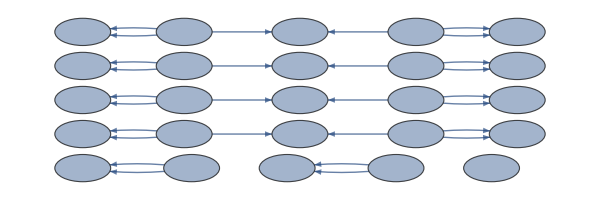
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→560,QCode→3103,RuleSet→{AA→,A→,→AA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→570,QCode→3123,RuleSet→{AA→,A→AA}|>: dead

<|Index→590,QCode→3213,RuleSet→{AA→A,→AA}|> (Repeating):

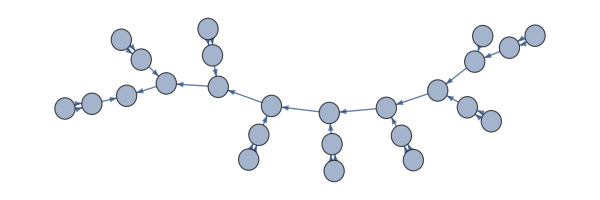
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→592,QCode→3220,RuleSet→{AA→A,A→,→A}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→600,QCode→3233,RuleSet→{AA→AAA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

<|Index→610,QCode→3303,RuleSet→{AAA→,→AA}|> (Repeating):

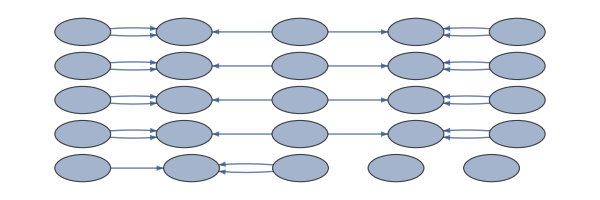
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→612,QCode→3310,RuleSet→{AAA→,A→,→A}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→618,QCode→3321,RuleSet→{AAA→A,→A}|> (Repeating):

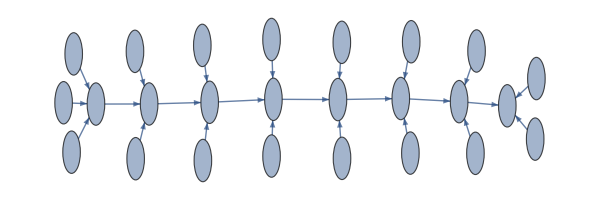
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→622,QCode→3330,RuleSet→{AAAA→,→A}|> (Repeating):

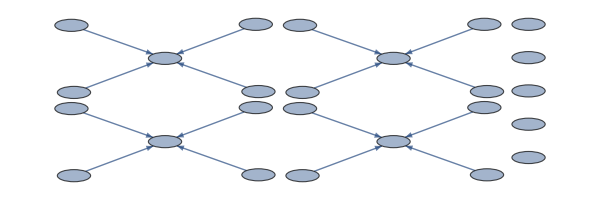
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1250,QCode→03333,RuleSet→{A→,→AAAAA}|> (Repeating):

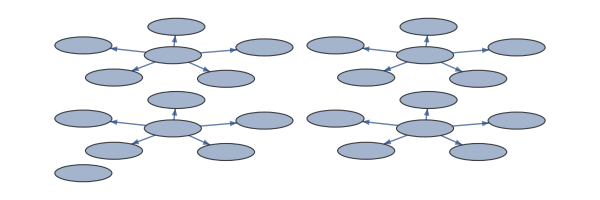
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1926,QCode→14034,RuleSet→{A→,B→,→AB}|> (Repeating):



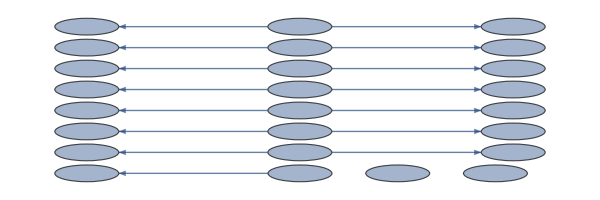
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1930,QCode→14043,RuleSet→{A→,B→,→BA}|> (Repeating):


-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1966,QCode→14214,RuleSet→{A→,B→A,→B}|> (Repeating):

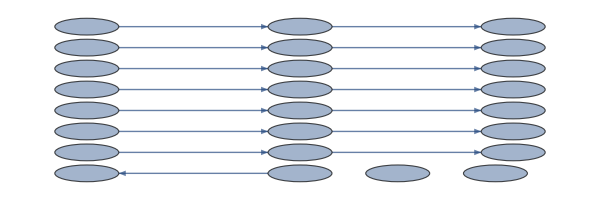
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1976,QCode→14234,RuleSet→{A→,B→AB}|> (Repeating):

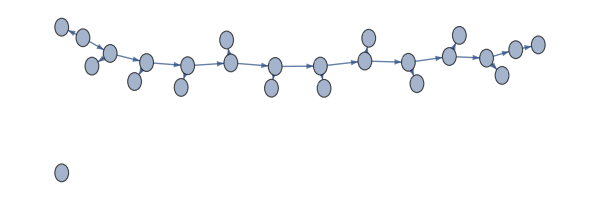
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1980,QCode→14243,RuleSet→{A→,B→BA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2602,QCode→24240,RuleSet→{A→B,B→,→A}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2604,QCode→24242,RuleSet→{A→B,B→A}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2750,QCode→30333,RuleSet→{AA→,→AAAA}|> (Repeating):

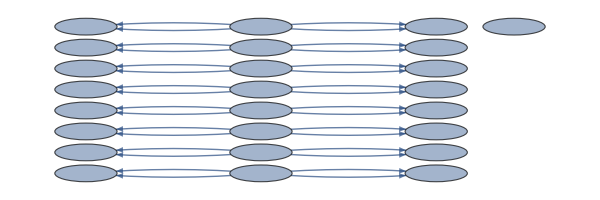
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2800,QCode→31033,RuleSet→{AA→,A→,→AAA}|> (Repeating):

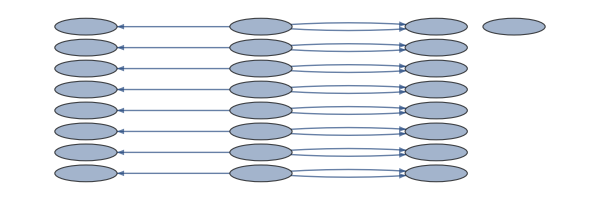
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2848,QCode→31231,RuleSet→{AA→,A→AA,→A}|> (Repeating):

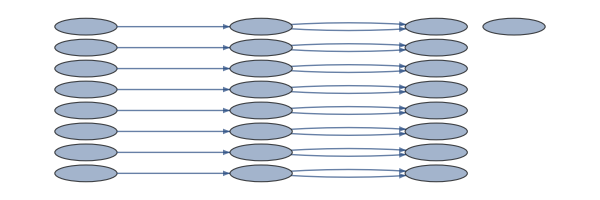
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2850,QCode→31233,RuleSet→{AA→,A→AAA}|>: dead

<|Index→2950,QCode→32133,RuleSet→{AA→A,→AAA}|> (Repeating):

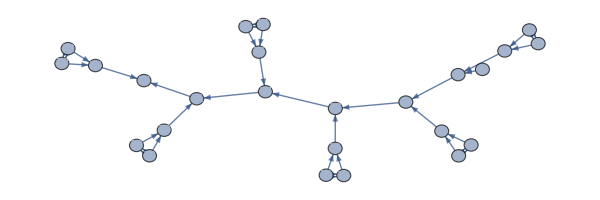
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2960,QCode→32203,RuleSet→{AA→A,A→,→AA}|> (Repeating):

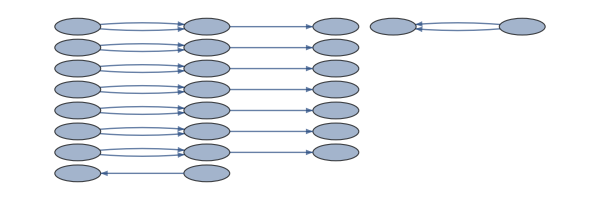
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2970,QCode→32223,RuleSet→{AA→A,A→AA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3050,QCode→33033,RuleSet→{AAA→,→AAA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3060,QCode→33103,RuleSet→{AAA→,A→,→AA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3070,QCode→33123,RuleSet→{AAA→,A→AA}|>: dead

<|Index→3072,QCode→33130,RuleSet→{AAA→,AA→,→A}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3090,QCode→33213,RuleSet→{AAA→A,→AA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3092,QCode→33220,RuleSet→{AAA→A,A→,→A}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3098,QCode→33231,RuleSet→{AAA→AA,→A}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3100,QCode→33233,RuleSet→{AAA→AAA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

<|Index→3110,QCode→33303,RuleSet→{AAAA→,→AA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3112,QCode→33310,RuleSet→{AAAA→,A→,→A}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3118,QCode→33321,RuleSet→{AAAA→A,→A}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3122,QCode→33330,RuleSet→{AAAAA→,→A}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3176,QCode→34034,RuleSet→{AB→,→AB}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3180,QCode→34043,RuleSet→{AB→,→BA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3216,QCode→34214,RuleSet→{AB→A,→B}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3226,QCode→34234,RuleSet→{AB→AB}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

<|Index→3228,QCode→34241,RuleSet→{AB→B,→A}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3230,QCode→34243,RuleSet→{AB→BA}|>: dead

<|Index→6250,QCode→033333,RuleSet→{A→,→AAAAAA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→9626,QCode→140334,RuleSet→{A→,B→,→AAB}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→9630,QCode→140343,RuleSet→{A→,B→,→ABA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→9650,QCode→140433,RuleSet→{A→,B→,→BAA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→9826,QCode→142134,RuleSet→{A→,B→A,→AB}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→9830,QCode→142143,RuleSet→{A→,B→A,→BA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→9866,QCode→142314,RuleSet→{A→,B→AA,→B}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→9876,QCode→142334,RuleSet→{A→,B→AAB}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→9878,QCode→142341,RuleSet→{A→,B→AB,→A}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→9880,QCode→142343,RuleSet→{A→,B→ABA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→9898,QCode→142431,RuleSet→{A→,B→BA,→A}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→9900,QCode→142433,RuleSet→{A→,B→BAA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
rs=FromReducedRankIndex[1];               (* or other desired starting point in the enumeration *)
While[rs["Index"]<10^4,                                                           (* or some large number, stopping point *)
If[(Length[ans=TestForAll[rs]])>0,rs=ans; Continue[]];  (* skip all that we can *)

(* do something with the rulesets that are not skipped *)
sss=SSS[rs["RuleSet"],25,Mode->Silent];  (* create the sessie for this ruleset *)
If[sss["Verdict"]==="Dead", Print[rs,": dead"],
(* else *) 
Print[rs," (",sss["Verdict"],"): "];
Print@SSSDisplay[sss,SSSMax->10,SSSSize->{50,100},NetSize->{600,200},VertexSize->0.8,VertexLabels->Placed[Automatic,Center]];
];
rs=FromReducedRankIndex[rs["Index"]+1]    (* increment *)
]
```

### Notes

It's amazing to be able to very rapidly jump over long subsequences of skippable cases, or discard cases with minimal time spent, but already in the first 10^5 cases, some needed improvements are clear:

1.  For repeating sessies, once the repetition has begun, it is desirable to cut off the beginning, non-repeating part.  (Restart the evolution, using an initial state taken from the repeating section, and then display that part.)

Ex/  #2, #10, #50, #110, ... : restart at 2

2.  It also might also be good to delete any initial state cells/letters that are never used, so as to simplify the sessie display.  Ex/ #1930

3.  Related idea:  in many cases some rules are only used a few times, and then never again.  If that could be reliably quantified, it would justify tossing the ruleset as a duplicate without bothering the human operator or even logging the case.  Ex/  #612, #3072, #3216

4.  So far, the majority of the cases that aren't recognized as "Dead" are "Repeating", and elsewhere we have code that can reliably create a summary of any repeating network (and many others).  It wouldn't be hard to add a function that checks a database of these summaries to see whether a given case is already in the list, and if not, add the new summary (with the index of the ruleset that created it) to the database.  Previously seen cases could then be silently treated without bothering the human operator.

5.  Many of the cases not recognized as "Dead" or "Repeating" generate no network or generate a previously seen network, perhaps after some initial stuff.  (This also relates to point (3) above.)  The sessie is generally growing without bound, but nothing new happens.  This begs for probabilistic-type tests on the network itself, to stop the evolution at some justifiable point and summarize the network, perhaps discarding or logging it.  Ex/ #20 {"A"→"AA"} builds the same 1-d chain as #4 {"A"→"A"}.

5.  Such network tests should identify cases such as "1-d", "2-d", "3-d", ..., "exponential", etc., and the "Verdict" should then be updated accordingly.

6.  If searching for "something new", cases with known "Verdict" could be tossed immediately.  If searching for particular examples of a particular "Verdict", all others could be tossed immediately (as is currently done with "Dead").

```mathematica
rs=FromReducedRankIndex[1];               (* or other desired starting point in the enumeration *)
While[rs["Index"]<10^5,                                                           (* or some large number, stopping point *)
If[(Length[ans=TestForAll[rs]])>0,rs=ans; Continue[]];  (* skip all that we can *)

(* do something with the rulesets that are not skipped *)
sss=SSS[rs["RuleSet"],25,Mode->Silent];  (* create the sessie for this ruleset *)
If[!MatchQ[sss["Verdict"],"Dead"|"Repeating"],
Print[rs," (",sss["Verdict"],"): "];
Print@SSSDisplay[sss,SSSMax->10,SSSSize->{50,100},NetSize->{600,200},VertexSize->0.8,VertexLabels->Placed[Automatic,Center]];
];
rs=FromReducedRankIndex[rs["Index"]+1]    (* increment *)
]
```

<|Index→20,QCode→23,RuleSet→{A→AA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

<|Index→600,QCode→3233,RuleSet→{AA→AAA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

<|Index→3216,QCode→34214,RuleSet→{AB→A,→B}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→13020,QCode→242423,RuleSet→{A→B,B→AA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→15500,QCode→332333,RuleSet→{AAA→AAAA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

<|Index→15676,QCode→334034,RuleSet→{AAB→,→AB}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→15680,QCode→334043,RuleSet→{AAB→,→BA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→15716,QCode→334214,RuleSet→{AAB→A,→B}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→15876,QCode→340334,RuleSet→{AB→,→AAB}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→15880,QCode→340343,RuleSet→{AB→,→ABA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→15900,QCode→340433,RuleSet→{AB→,→BAA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→15980,QCode→341243,RuleSet→{AB→,A→BA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→16076,QCode→342134,RuleSet→{AB→A,→AB}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→16080,QCode→342143,RuleSet→{AB→A,→BA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→16086,QCode→342204,RuleSet→{AB→A,A→,→B}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→16116,QCode→342314,RuleSet→{AB→AA,→B}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→16126,QCode→342334,RuleSet→{AB→AAB}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

<|Index→16130,QCode→342343,RuleSet→{AB→ABA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

<|Index→16148,QCode→342431,RuleSet→{AB→BA,→A}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→16176,QCode→343034,RuleSet→{ABA→,→AB}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→16180,QCode→343043,RuleSet→{ABA→,→BA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→16216,QCode→343214,RuleSet→{ABA→A,→B}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→16228,QCode→343241,RuleSet→{ABA→B,→A}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→49401,QCode→1423434,RuleSet→{A→,B→ABB}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→49501,QCode→1424334,RuleSet→{A→,B→BAB}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→49503,QCode→1424341,RuleSet→{A→,B→BB,→A}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→49505,QCode→1424343,RuleSet→{A→,B→BBA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→65098,QCode→2424231,RuleSet→{A→B,B→AA,→A}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→65100,QCode→2424233,RuleSet→{A→B,B→AAA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→65101,QCode→2424234,RuleSet→{A→B,B→AB}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→65105,QCode→2424243,RuleSet→{A→B,B→BA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→65729,QCode→2434242,RuleSet→{A→BB,B→A}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→71966,QCode→3134214,RuleSet→{AA→,AB→A,→B}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→74386,QCode→3223404,RuleSet→{AA→A,AB→,→B}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→74486,QCode→3224304,RuleSet→{AA→A,BA→,→B}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→75522,QCode→3242430,RuleSet→{AA→B,BA→,→A}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→78176,QCode→3334034,RuleSet→{AAAB→,→AB}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→78180,QCode→3334043,RuleSet→{AAAB→,→BA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→78216,QCode→3334214,RuleSet→{AAAB→A,→B}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→78426,QCode→3341034,RuleSet→{AAB→,A→,→AB}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→78430,QCode→3341043,RuleSet→{AAB→,A→,→BA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→78476,QCode→3341234,RuleSet→{AAB→,A→AB}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→78478,QCode→3341241,RuleSet→{AAB→,A→B,→A}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→78480,QCode→3341243,RuleSet→{AAB→,A→BA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→78576,QCode→3342134,RuleSet→{AAB→A,→AB}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→78580,QCode→3342143,RuleSet→{AAB→A,→BA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→78586,QCode→3342204,RuleSet→{AAB→A,A→,→B}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→78616,QCode→3342314,RuleSet→{AAB→AA,→B}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→78648,QCode→3342431,RuleSet→{AAB→BA,→A}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→78676,QCode→3343034,RuleSet→{AABA→,→AB}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→78680,QCode→3343043,RuleSet→{AABA→,→BA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→78716,QCode→3343214,RuleSet→{AABA→A,→B}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→78728,QCode→3343241,RuleSet→{AABA→B,→A}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→79376,QCode→3403334,RuleSet→{AB→,→AAAB}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→79380,QCode→3403343,RuleSet→{AB→,→AABA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→79400,QCode→3403433,RuleSet→{AB→,→ABAA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→79401,QCode→3403434,RuleSet→{AB→,→ABB}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→79500,QCode→3404333,RuleSet→{AB→,→BAAA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→79501,QCode→3404334,RuleSet→{AB→,→BAB}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→79505,QCode→3404343,RuleSet→{AB→,→BBA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→79866,QCode→3412314,RuleSet→{AB→,A→AA,→B}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→79898,QCode→3412431,RuleSet→{AB→,A→BA,→A}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→79900,QCode→3412433,RuleSet→{AB→,A→BAA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→79966,QCode→3413214,RuleSet→{AB→,AA→A,→B}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→80055,QCode→3414043,RuleSet→{AB→,B→,→BA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→80091,QCode→3414214,RuleSet→{AB→,B→A,→B}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→80376,QCode→3421334,RuleSet→{AB→A,→AAB}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→80380,QCode→3421343,RuleSet→{AB→A,→ABA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→80400,QCode→3421433,RuleSet→{AB→A,→BAA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→80401,QCode→3421434,RuleSet→{AB→A,→BB}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→80480,QCode→3422243,RuleSet→{AB→A,A→BA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→80486,QCode→3422304,RuleSet→{AB→A,AA→,→B}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→80576,QCode→3423134,RuleSet→{AB→AA,→AB}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→80580,QCode→3423143,RuleSet→{AB→AA,→BA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→80586,QCode→3423204,RuleSet→{AB→AA,A→,→B}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→80616,QCode→3423314,RuleSet→{AB→AAA,→B}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→80626,QCode→3423334,RuleSet→{AB→AAAB}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

<|Index→80701,QCode→3424134,RuleSet→{AB→B,→AB}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→80705,QCode→3424143,RuleSet→{AB→B,→BA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→80720,QCode→3424223,RuleSet→{AB→B,A→AA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→80727,QCode→3424240,RuleSet→{AB→B,B→,→A}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→80740,QCode→3424313,RuleSet→{AB→BA,→AA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→80741,QCode→3424314,RuleSet→{AB→BA,→B}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→80748,QCode→3424331,RuleSet→{AB→BAA,→A}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→80751,QCode→3424334,RuleSet→{AB→BAB}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

<|Index→80753,QCode→3424341,RuleSet→{AB→BB,→A}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→80926,QCode→3431034,RuleSet→{ABA→,A→,→AB}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→80930,QCode→3431043,RuleSet→{ABA→,A→,→BA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→80976,QCode→3431234,RuleSet→{ABA→,A→AB}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→80978,QCode→3431241,RuleSet→{ABA→,A→B,→A}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→80980,QCode→3431243,RuleSet→{ABA→,A→BA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→81086,QCode→3432204,RuleSet→{ABA→A,A→,→B}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→81116,QCode→3432314,RuleSet→{ABA→AA,→B}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→81128,QCode→3432341,RuleSet→{ABA→AB,→A}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→81140,QCode→3432413,RuleSet→{ABA→B,→AA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→81148,QCode→3432431,RuleSet→{ABA→BA,→A}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→81176,QCode→3433034,RuleSet→{ABAA→,→AB}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→81180,QCode→3433043,RuleSet→{ABAA→,→BA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→81216,QCode→3433214,RuleSet→{ABAA→A,→B}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→81228,QCode→3433241,RuleSet→{ABAA→B,→A}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→81301,QCode→3434034,RuleSet→{ABB→,→AB}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→81305,QCode→3434043,RuleSet→{ABB→,→BA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→81341,QCode→3434214,RuleSet→{ABB→A,→B}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→81353,QCode→3434241,RuleSet→{ABB→B,→A}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

Take a closer look at that last one:

```mathematica
sss["RuleSet"]
```

{ABB→B,→A}

```mathematica
sss=SSS[{"ABB"->"B",""->"A"},25,SSSSize->100,SSSMax->10,NetSize->600];
```

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

Nothing interesting happens after step 3.

```mathematica
sss["Evolution"]⟦3⟧
```

BA

We could re-evolve from that point on, but that requires human intervention.  Automatic identification is still an issue.  Could the sessie or its network be ID'd by the network not continuing?

```mathematica
sss["Net"]
```

{1→2}

Or by the repeating pattern in its connection list or list of rules used?

```mathematica
sss["ConnectionList"]
```

{{3,4,5}→{7},{1,2,7}→{8},{}→{9},{}→{10},{}→{11},{}→{12},{}→{13},{}→{14},{}→{15},{}→{16},{}→{17},{}→{18},{}→{19},{}→{20},{}→{21},{}→{22},{}→{23},{}→{24},{}→{25},{}→{26},{}→{27},{}→{28},{}→{29},{}→{30},{}→{31}}

```mathematica
sss["RulesUsed"]
```

{1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

Both of these show a 1-d pattern starting at step 3.  How many steps should be taken before we can justifiably discard the beginning, and deciding to skip it or proceeding with summarizing and identification?

Elsewhere I argue that the pattern should repeat at least 6 times (but maybe 10 would be safer), and should include all of the last 90%.  The danger is that a temporary pattern might trigger a premature decision.

In this case, such a test could be combined with a rule (1) never being used again to trigger skipping this case as a duplicate.

But actually even the simpler {""→"A"} (not included in the RSS enumeration) produces a null network:

```mathematica
SSS[{""->"A"},"",10,SSSSize->100,NetSize->600];
```

-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

Similarly, {"A"→"AA"} gives the same network (but a different sessie and connection list) as {"A"→"A"}:

```mathematica
sss1d=SSS[{"A"->"AA"},"A",10,SSSSize->100,NetSize->600];
sss1d["Net"]
sss1d["ConnectionList"]
```

-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→9,9→10}

{{1}→{2,3},{2}→{4,5},{4}→{6,7},{6}→{8,9},{8}→{10,11},{10}→{12,13},{12}→{14,15},{14}→{16,17},{16}→{18,19},{18}→{20,21}}

```mathematica
SSS[{"A"->"A"},"A",10,SSSSize->{50,200},NetSize->600];
%["Net"]
%%["ConnectionList"]
```

-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→9,9→10}

{{1}→{2},{2}→{3},{3}→{4},{4}→{5},{5}→{6},{6}→{7},{7}→{8},{8}→{9},{9}→{10},{10}→{11}}